```mathematica
Assuming[l>0,DSolve[D[r^2 D[R[r],r],r]-2l(l+1)R[r]== κ μ^2 SphericalBesselJ[l,k r]^2, R,r]]
```

{{R→Function[{r},r^((ⅈ √(l (1+l)) (ⅈ/(√2 √(l (1+l)))-ⅈ √(4+1/(2 l (1+l)))))/(√2)) C[1]+r^((ⅈ √(l (1+l)) (ⅈ/(√2 √(l (1+l)))+ⅈ √(4+1/(2 l (1+l)))))/(√2)) C[2]-(2^(-1-2 l) π r^(1/2-1/2 √(1+8 l+8 l^2)) (k r)^(2 l) κ μ^2 (-r^((ⅈ √(l (1+l)) (ⅈ/(√2 √(l (1+l)))-(ⅈ √(-(-1-8 l-8 l^2)/(l (1+l))))/(√2)))/(√2)) HypergeometricPFQ[{1+l,1/4+l-1/4 √(1+8 l+8 l^2)},{3/2+l,2+2 l,5/4+l-1/4 √(1+8 l+8 l^2)},-k^2 r^2]-4 l r^((ⅈ √(l (1+l)) (ⅈ/(√2 √(l (1+l)))-(ⅈ √(-(-1-8 l-8 l^2)/(l (1+l))))/(√2)))/(√2)) HypergeometricPFQ[{1+l,1/4+l-1/4 √(1+8 l+8 l^2)},{3/2+l,2+2 l,5/4+l-1/4 √(1+8 l+8 l^2)},-k^2 r^2]-√(1+8 l+8 l^2) r^((ⅈ √(l (1+l)) (ⅈ/(√2 √(l (1+l)))-(ⅈ √(-(-1-8 l-8 l^2)/(l (1+l))))/(√2)))/(√2)) HypergeometricPFQ[{1+l,1/4+l-1/4 √(1+8 l+8 l^2)},{3/2+l,2+2 l,5/4+l-1/4 √(1+8 l+8 l^2)},-k^2 r^2]+r^(√(1+8 l+8 l^2)+(ⅈ √(l (1+l)) (ⅈ/(√2 √(l (1+l)))+(ⅈ √(-(-1-8 l-8 l^2)/(l (1+l))))/(√2)))/(√2)) HypergeometricPFQ[{1+l,1/4+l+1/4 √(1+8 l+8 l^2)},{3/2+l,2+2 l,5/4+l+1/4 √(1+8 l+8 l^2)},-k^2 r^2]+4 l r^(√(1+8 l+8 l^2)+(ⅈ √(l (1+l)) (ⅈ/(√2 √(l (1+l)))+(ⅈ √(-(-1-8 l-8 l^2)/(l (1+l))))/(√2)))/(√2)) HypergeometricPFQ[{1+l,1/4+l+1/4 √(1+8 l+8 l^2)},{3/2+l,2+2 l,5/4+l+1/4 √(1+8 l+8 l^2)},-k^2 r^2]-√(1+8 l+8 l^2) r^(√(1+8 l+8 l^2)+(ⅈ √(l (1+l)) (ⅈ/(√2 √(l (1+l)))+(ⅈ √(-(-1-8 l-8 l^2)/(l (1+l))))/(√2)))/(√2)) HypergeometricPFQ[{1+l,1/4+l+1/4 √(1+8 l+8 l^2)},{3/2+l,2+2 l,5/4+l+1/4 √(1+8 l+8 l^2)},-k^2 r^2]))/(√(1+8 l+8 l^2) (1+4 l-√(1+8 l+8 l^2)) (1+4 l+√(1+8 l+8 l^2)) Gamma[3/2+l]^2)]}}

```mathematica
Simplify[r^((ⅈ √(l (1+l)) (ⅈ/(√2 √(l (1+l)))-ⅈ √(4+1/(2 l (1+l)))))/(√2)) C[1]+r^((ⅈ √(l (1+l)) (ⅈ/(√2 √(l (1+l)))+ⅈ √(4+1/(2 l (1+l)))))/(√2)) C[2]-(2^(-1-2 l) π r^(1/2-1/2 √(1+8 l+8 l^2)) (k r)^(2 l) κ μ^2 (-r^((ⅈ √(l (1+l)) (ⅈ/(√2 √(l (1+l)))-(ⅈ √(-(-1-8 l-8 l^2)/(l (1+l))))/(√2)))/(√2)) HypergeometricPFQ[{1+l,1/4+l-1/4 √(1+8 l+8 l^2)},{3/2+l,2+2 l,5/4+l-1/4 √(1+8 l+8 l^2)},-k^2 r^2]-4 l r^((ⅈ √(l (1+l)) (ⅈ/(√2 √(l (1+l)))-(ⅈ √(-(-1-8 l-8 l^2)/(l (1+l))))/(√2)))/(√2)) HypergeometricPFQ[{1+l,1/4+l-1/4 √(1+8 l+8 l^2)},{3/2+l,2+2 l,5/4+l-1/4 √(1+8 l+8 l^2)},-k^2 r^2]-√(1+8 l+8 l^2) r^((ⅈ √(l (1+l)) (ⅈ/(√2 √(l (1+l)))-(ⅈ √(-(-1-8 l-8 l^2)/(l (1+l))))/(√2)))/(√2)) HypergeometricPFQ[{1+l,1/4+l-1/4 √(1+8 l+8 l^2)},{3/2+l,2+2 l,5/4+l-1/4 √(1+8 l+8 l^2)},-k^2 r^2]+r^(√(1+8 l+8 l^2)+(ⅈ √(l (1+l)) (ⅈ/(√2 √(l (1+l)))+(ⅈ √(-(-1-8 l-8 l^2)/(l (1+l))))/(√2)))/(√2)) HypergeometricPFQ[{1+l,1/4+l+1/4 √(1+8 l+8 l^2)},{3/2+l,2+2 l,5/4+l+1/4 √(1+8 l+8 l^2)},-k^2 r^2]+4 l r^(√(1+8 l+8 l^2)+(ⅈ √(l (1+l)) (ⅈ/(√2 √(l (1+l)))+(ⅈ √(-(-1-8 l-8 l^2)/(l (1+l))))/(√2)))/(√2)) HypergeometricPFQ[{1+l,1/4+l+1/4 √(1+8 l+8 l^2)},{3/2+l,2+2 l,5/4+l+1/4 √(1+8 l+8 l^2)},-k^2 r^2]-√(1+8 l+8 l^2) r^(√(1+8 l+8 l^2)+(ⅈ √(l (1+l)) (ⅈ/(√2 √(l (1+l)))+(ⅈ √(-(-1-8 l-8 l^2)/(l (1+l))))/(√2)))/(√2)) HypergeometricPFQ[{1+l,1/4+l+1/4 √(1+8 l+8 l^2)},{3/2+l,2+2 l,5/4+l+1/4 √(1+8 l+8 l^2)},-k^2 r^2]))/(√(1+8 l+8 l^2) (1+4 l-√(1+8 l+8 l^2)) (1+4 l+√(1+8 l+8 l^2)) Gamma[3/2+l]^2)]
```

```mathematica
Assuming[l>0,Simplify[1/(l^2 √(1+8 l+8 l^2) Gamma[3/2+l]^2)4^(-2-l) r^(1/2 (-1-√(1+8 l+8 l^2)-√(l (1+l)) √((1+8 l+8 l^2)/(l+l^2)))) ((1+4 l+√(1+8 l+8 l^2)) π r^(1/2+√(l (1+l)) √((1+8 l+8 l^2)/(l+l^2))) (k r)^(2 l) κ μ^2 HypergeometricPFQ[{1+l,1/4+l-1/4 √(1+8 l+8 l^2)},{3/2+l,2+2 l,5/4+l-1/4 √(1+8 l+8 l^2)},-k^2 r^2]+r^(1/2 √(1+8 l+8 l^2)) (4^(2+l) l^2 √(1+8 l+8 l^2) (r^(√(l (1+l)) √((1+8 l+8 l^2)/(l+l^2))) C[1]+C[2]) Gamma[3/2+l]^2+(-1-4 l+√(1+8 l+8 l^2)) π r^(1/2 (1+√(1+8 l+8 l^2))) (k r)^(2 l) κ μ^2 HypergeometricPFQ[{1+l,1/4+l+1/4 √(1+8 l+8 l^2)},{3/2+l,2+2 l,5/4+l+1/4 √(1+8 l+8 l^2)},-k^2 r^2]))]]
```

```mathematica
Rr[l_,r_]:=- r^(-1/2-1/2 √(1+8 l+8 l^2))+(4^(-2-l) π (k r)^(2 l) κ μ^2)/(l^2 √(1+8 l+8 l^2) Gamma[3/2+l]^2) ((1+4 l+√(1+8 l+8 l^2))  HypergeometricPFQ[{1+l,1/4+l-1/4 √(1+8 l+8 l^2)},{3/2+l,2+2 l,5/4+l-1/4 √(1+8 l+8 l^2)},-k^2 r^2]+(-1-4 l+√(1+8 l+8 l^2)) HypergeometricPFQ[{1+l,1/4+l+1/4 √(1+8 l+8 l^2)},{3/2+l,2+2 l,5/4+l+1/4 √(1+8 l+8 l^2)},-k^2 r^2])
```

```mathematica
Rrr[l_,r_]:=1/(l^2 √(1+8 l+8 l^2) Gamma[3/2+l]^2)4^(-2-l) (4^(2+l) l^2 √(1+8 l+8 l^2) r^(-1/2-1/2 √(1+8 l+8 l^2)) (r^(√(1+8 l+8 l^2)) C1+C2) Gamma[3/2+l]^2+(1+4 l+√(1+8 l+8 l^2)) π (k r)^(2 l) κ μ^2 HypergeometricPFQ[{1+l,1/4+l-1/4 √(1+8 l+8 l^2)},{3/2+l,2+2 l,5/4+l-1/4 √(1+8 l+8 l^2)},-k^2 r^2]+(-1-4 l+√(1+8 l+8 l^2)) π (k r)^(2 l) κ μ^2 HypergeometricPFQ[{1+l,1/4+l+1/4 √(1+8 l+8 l^2)},{3/2+l,2+2 l,5/4+l+1/4 √(1+8 l+8 l^2)},-k^2 r^2])
```

```mathematica
Needs["MaTeX`"]
MaTeX["\\int\\frac{i x^2}{i+x^2}dx"]
κ=8 π G/c^4;
G=1;
c=1;
μ=15.614 (*[1/pc]*)
ω=μ-.1*μ;
k= μ ω
ri = 0.0001;
rf = 100;
C1= 0;
C2= -1;
```

-Graphics-

15.614

219.417

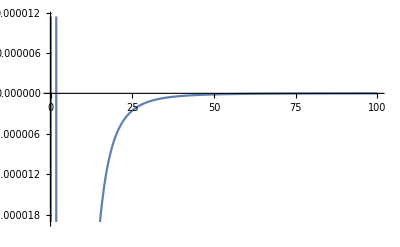

```mathematica
Plot[Rr[2,r],{r,10 ri,rf}]
```

Ecuación a resolver:

```mathematica
eceins=D[Sin[θ] D[F[r,θ],θ],θ]+Sin[θ]D[r^2 D[F[r,θ],r],r]== -2 Sin[θ] Rr[l,r] LegendreP[l,1,Cos[θ]]^2;
```

```mathematica
efe=ParametricNDSolveValue[{eceins,DirichletCondition[F[r,θ]==-1/r,θ==π/2]},F,{r,ri,rf},{θ,0,π},l,DependentVariables->{F},InterpolationOrder->All,MaxStepFraction->1/100]
```

ParametricFunction[<>]

```mathematica
Plot3D[efe[2][r,θ],{r,2,rf},{θ,0,π},AxesLabel->MaTeX /@{"r","\\theta","F"},PlotRange->Automatic,PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[Evaluate[Table[{efe[l][r,θ]},{l,1,3}]],{r,2,rf},{θ,0,π},AxesLabel->MaTeX /@{"r","\\theta","F"},PlotRange->Automatic,PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[Rr[2,r] LegendreP[2,Cos[θ]]^2+efe[2][r,θ],{r,2,rf},{θ,0,π},AxesLabel->MaTeX /@{"r","\\theta","\\psi_2"},PlotRange->Automatic,PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[Rr[2,r] LegendreP[2,Cos[θ]]^2,{r,2,rf},{θ,0,π},AxesLabel->MaTeX /@{"r","\\theta","R_l(r) P_l(\\cos\\theta)^2"},PlotRange->Automatic,PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Assuming[a>0,DSolve[D[r^2 D[R[r],r],r]-2a(a+1) R[r]==0, R,r]]
```

{{R→Function[{r},r^((ⅈ √(a (1+a)) (ⅈ/(√2 √(a (1+a)))-ⅈ √(4+1/(2 a (1+a)))))/(√2)) C[1]+r^((ⅈ √(a (1+a)) (ⅈ/(√2 √(a (1+a)))+ⅈ √(4+1/(2 a (1+a)))))/(√2)) C[2]]}}

```mathematica
T3[a_,r_]:=r^(-1/2+1/2 √(8a (1+a)+1))
```

```mathematica
T4[a_,r_]:=r^(-1/2-1/2 √(8a (1+a)+1))
```

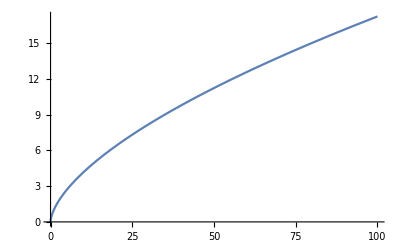

```mathematica
Plot[T1[1,r],{r,ri,rf}]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1+1/4 (5-√17)+1/4 (-9+√17).

General::stop: Further output of N::meprec will be suppressed during this calculation.

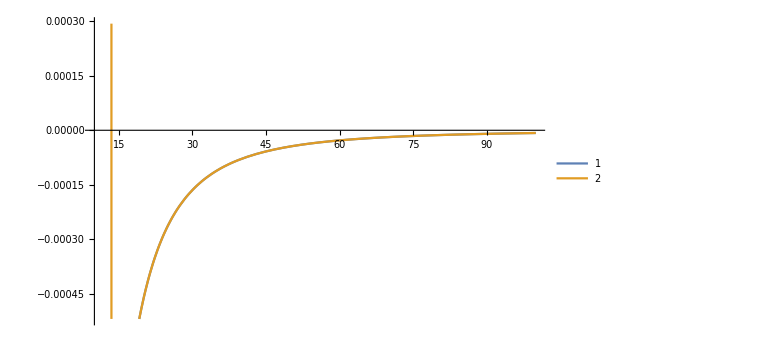

```mathematica
Plot[{Evaluate[Table[-T2[a,r],{a,{2}}]],Rr[1,r]},{r,10,rf},PlotLegends->Automatic,ImageSize->Large]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1+1/4 (5-√17)+1/4 (-9+√17).

General::stop: Further output of N::meprec will be suppressed during this calculation.

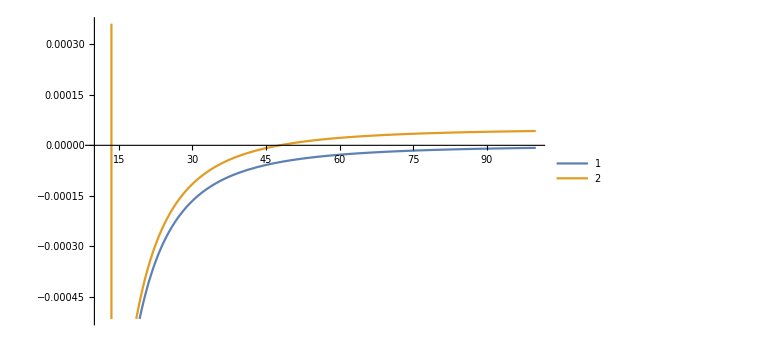

```mathematica
Plot[{-T4[1,r],Rr[1,r]+.00005},{r,10,rf},PlotLegends->Automatic,ImageSize->Large]
```

```mathematica
Assuming[a>0,DSolve[D[(1-x^2)D[Y[x],x],x]+2 LegendreP[l,1,x]^2==2l(l+1) Y[x],Y,x]]
```

{{Y→Function[{x},C[1] LegendreP[1/2 (-1+√(1-8 l-8 l^2)),x]+(∫_1^x ((LegendreP[l,1,K[1]]^2 LegendreQ[1/2 (-1+√(1-8 l-8 l^2)),K[1]])/(2 l (1+l) (LegendreP[1/2 (1+√(1-8 l (1+l))),K[1]] LegendreQ[1/2 (-1+√(1-8 l (1+l))),K[1]]-LegendreP[1/2 (-1+√(1-8 l (1+l))),K[1]] LegendreQ[1/2 (1+√(1-8 l (1+l))),K[1]]))-(√(1-8 l-8 l^2) LegendreP[l,1,K[1]]^2 LegendreQ[1/2 (-1+√(1-8 l-8 l^2)),K[1]])/(2 l (1+l) (LegendreP[1/2 (1+√(1-8 l (1+l))),K[1]] LegendreQ[1/2 (-1+√(1-8 l (1+l))),K[1]]-LegendreP[1/2 (-1+√(1-8 l (1+l))),K[1]] LegendreQ[1/2 (1+√(1-8 l (1+l))),K[1]])))ⅆK[1]) LegendreP[1/2 (-1+√(1-8 l-8 l^2)),x]+C[2] LegendreQ[1/2 (-1+√(1-8 l-8 l^2)),x]+(∫_1^x (-((LegendreP[1/2 (-1+√(1-8 l-8 l^2)),K[2]] LegendreP[l,1,K[2]]^2)/(2 l (1+l) (LegendreP[1/2 (1+√(1-8 l (1+l))),K[2]] LegendreQ[1/2 (-1+√(1-8 l (1+l))),K[2]]-LegendreP[1/2 (-1+√(1-8 l (1+l))),K[2]] LegendreQ[1/2 (1+√(1-8 l (1+l))),K[2]])))+(√(1-8 l-8 l^2) LegendreP[1/2 (-1+√(1-8 l-8 l^2)),K[2]] LegendreP[l,1,K[2]]^2)/(2 l (1+l) (LegendreP[1/2 (1+√(1-8 l (1+l))),K[2]] LegendreQ[1/2 (-1+√(1-8 l (1+l))),K[2]]-LegendreP[1/2 (-1+√(1-8 l (1+l))),K[2]] LegendreQ[1/2 (1+√(1-8 l (1+l))),K[2]])))ⅆK[2]) LegendreQ[1/2 (-1+√(1-8 l-8 l^2)),x]]}}

```mathematica
Simplify[C[1] LegendreP[1/2 (-1+√(1-8 l-8 l^2)),x]+(∫_1^x ((LegendreP[l,1,K[1]]^2 LegendreQ[1/2 (-1+√(1-8 l-8 l^2)),K[1]])/(2 l (1+l) (LegendreP[1/2 (1+√(1-8 l (1+l))),K[1]] LegendreQ[1/2 (-1+√(1-8 l (1+l))),K[1]]-LegendreP[1/2 (-1+√(1-8 l (1+l))),K[1]] LegendreQ[1/2 (1+√(1-8 l (1+l))),K[1]]))-(√(1-8 l-8 l^2) LegendreP[l,1,K[1]]^2 LegendreQ[1/2 (-1+√(1-8 l-8 l^2)),K[1]])/(2 l (1+l) (LegendreP[1/2 (1+√(1-8 l (1+l))),K[1]] LegendreQ[1/2 (-1+√(1-8 l (1+l))),K[1]]-LegendreP[1/2 (-1+√(1-8 l (1+l))),K[1]] LegendreQ[1/2 (1+√(1-8 l (1+l))),K[1]])))ⅆK[1]) LegendreP[1/2 (-1+√(1-8 l-8 l^2)),x]]
```

(C[1]+∫_1^x -(((-1+√(1-8 l-8 l^2)) LegendreP[l,1,K[1]]^2 LegendreQ[1/2 (-1+√(1-8 l-8 l^2)),K[1]])/(2 l (1+l) (LegendreP[1/2 (1+√(1-8 l (1+l))),K[1]] LegendreQ[1/2 (-1+√(1-8 l (1+l))),K[1]]-LegendreP[1/2 (-1+√(1-8 l (1+l))),K[1]] LegendreQ[1/2 (1+√(1-8 l (1+l))),K[1]])))ⅆK[1]) LegendreP[1/2 (-1+√(1-8 l-8 l^2)),x]

```mathematica
θθ[l_,x_]:=(C11+∫_1^x -(((-1+√(1-8 l-8 l^2)) LegendreP[l,1,K[1]]^2 LegendreQ[1/2 (-1+√(1-8 l-8 l^2)),K[1]])/(2 l (1+l) (LegendreP[1/2 (1+√(1-8 l (1+l))),K[1]] LegendreQ[1/2 (-1+√(1-8 l (1+l))),K[1]]-LegendreP[1/2 (-1+√(1-8 l (1+l))),K[1]] LegendreQ[1/2 (1+√(1-8 l (1+l))),K[1]])))ⅆK[1]) LegendreP[1/2 (-1+√(1-8 l-8 l^2)),x]
```

```mathematica
lm[l_,x_]:=∫_1^x -(((-1+√(1-8 l-8 l^2)) LegendreP[l,1,y]^2 LegendreQ[1/2 (-1+√(1-8 l-8 l^2)),y])/(2 l (1+l) (LegendreP[1/2 (1+√(1-8 l (1+l))),y] LegendreQ[1/2 (-1+√(1-8 l (1+l))),y]-LegendreP[1/2 (-1+√(1-8 l (1+l))),y] LegendreQ[1/2 (1+√(1-8 l (1+l))),y])))ⅆy
```

```mathematica
C11=1
```

1

```mathematica
Evaluate[lm[2,-1]]
```

$Aborted

```mathematica
Plot[θθ[2,x],{x,-1,1}]
```

$Aborted

```mathematica
Evaluate[Table[θθ[1,x],{x,-1,1,1}]]
```

{θθ[1,-1],θθ[1,0],θθ[1,1]}